```mathematica
(* The idea here is to plot my function as a 3D density plot *)
```

```mathematica
(* kap=4.05
phi=0.6
testf[Pe_]:=3*Pi^2*kap/(4*0.6*Pe)
Plot[testf[x],{x,0,500},PlotRange->{0,1}] *)
```

```mathematica
(* Solve[(3*Pi^2*kappa)/(4*phi*xa*(PeA-PeB)+PeB)==1,xa] *)
```

```mathematica
(* xa=0.5
kappa=3.5
constxa[PeA_,PeB_]:=(3*Pi^2*kappa)/(4*phi*(xa*(PeA-PeB)+PeB))
f[PeA_,PeB_]:=If[PeA+PeB>=(3*Pi^2*kappa)/(4*phi*xa),Abs[1-constxa[PeA,PeB]],0]
Plot3D[f[PeA,PeB],{PeA,0,150},{PeB,0,150}]
DensityPlot[f[PeA,PeB],{PeA,0,150},{PeB,0,150}] *)
(* ContourPlot[f[PeA,PeB],{PeA,0,150},{PeB,0,150},Contours->10,ContourLabels->False,PlotLegends->Automatic,Exclusions->None] *)
```

```mathematica
phi=0.6
kappa=2.0
myf[PeA_,PeB_,xa_]:=(3*Pi^2*kappa)/(4*phi*(xa*(PeA-PeB)+PeB))
(* also try Abs[1-myf[PeA,PeB,xa]] *)
myiff[PeA_,PeB_,xa_]:=If[(xa*PeA+PeB-PeB*xa)>((3*kappa*Pi^2)/(4*phi)),myf[PeA,PeB,xa],1]
myabsiff[PeA_,PeB_,xa_]:=If[(xa*PeA+PeB-PeB*xa)>((3*kappa*Pi^2)/(4*phi)),Abs[1-myf[PeA,PeB,xa]],0]
(* DensityPlot3D[myiff[PeA,PeB,xa],{PeA,0,150},{PeB,0,150},{xa,0,1}] *)
ContourPlot3D[myiff[PeA,PeB,xa],{PeA,0,150},{PeB,0,150},{xa,0,1},Contours->1,ContourStyle->Opacity[0.5],AxesLabel->{Pe_A,Pe_B,x_a},PlotLegends->Automatic];
```

0.6

2.

```mathematica
(*ContourPlot[myf[PeA,45,xa],{PeA,0,150},{xa,0,1.0},ColorFunction->"Rainbow",Contours->20,PlotLegends->All,PlotRange->{0,1}]*)
```

```mathematica
data=Partition[Import["/Users/kolbt/Desktop/phase_3D.txt","Table"],{11, 16}];
(* ListPlot3D[data, Mesh->All] *)
mymat = MatrixForm[data];
(* This gives each PeB plane *)
mymat[[1,1, 1]];
mymat[[1,2, 1]];
mymat[[1,16, 1]];
(* This gives xa=1 of a given plane *)
mymat[[1,16,1, 1]];
(* This gives xa=0 peA=150 of peB=150 *)
mymat[[1,16,1,11,16]];
(* Ranges:
	PeA = 1 : 16, PeB = 1 : 16, xA = 1 : 11
		mymat[[1, PeB, 1, xA, PeA]]
		mat3d[[PeB, PeA, xA]]
*)
```

```mathematica
mat3d=ConstantArray[0,{16,16,11}];
For[i=1,i<17,++i,
For[j=1,j<17, ++j,
For[k=1,k<12,++k,mat3d[[i,j,k]]=mymat[[1,i,1,k,j]]]]]
```

```mathematica
(* Attempting to plot things here *)
p1 = ContourPlot3D[myiff[(PeA)*10,(PeB)*10,(xa)/10],{PeA,-0.5,15.5},{PeB,-0.5,15.5},{xa,-0.5,10.5},Contours->{0.5},ContourStyle->Opacity[0.8],AxesLabel->{Pe_A,Pe_B,x_a},PlotLegends->Automatic];
p2 = Graphics3D[First@Last@Reap[MapIndexed[If[#==1,Sow[Cuboid[#2]]]&,mat3d,-1]]];
Show[p1,p2];
```

```mathematica
bM = mat3d /. x_ -> UnitStep[x-.5];
p3= Table[Graphics3D[{Hue[1/3,1,1,.5],{Opacity[1],Cuboid[#]}&/@Position[bM,1]}]];
Show[p1,p3];
```

```mathematica
(*cubefunc[i_,j_,k_]:=If[mat3d[[i,j,k]]==1,Cuboid[{i-0.5,j-0.5,k-0.5}],-1]
Graphics3D[
For[i=1,i<17,++i,
For[j=1,j<17, ++j,
For[k=1,k<12,++k,
cubefunc[i,j,k]]]]]*)
```

```mathematica
p4= Graphics3D[First@Last@Reap[MapIndexed[If[#==1,Sow[{Opacity[0.8],Cuboid[#2-1.5]}]]&,mat3d,-1]]];
Show[p1,p4];
```

```mathematica
(* 
I want to plot this same thing on individual 2D planes, just keep PeB constant!
*)
```

0.0000884474

1.

-Graphics3D-

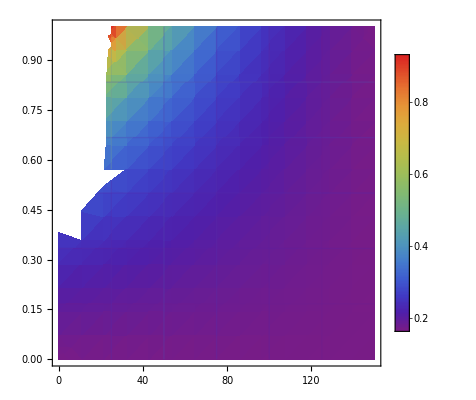

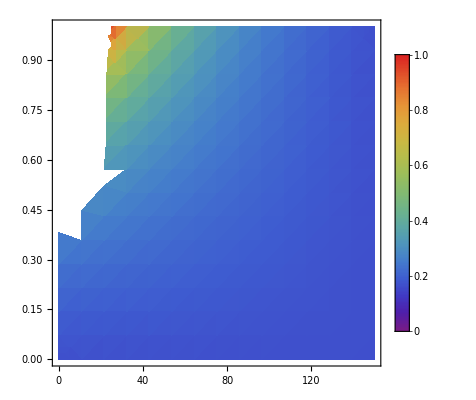

1

0.268196

0.98696

0.165597

```mathematica
min=FindMinValue[{myiff[PeA,150,xa],PeA<150,xa<150},{PeA,xa}]
max=FindMaxValue[{myiff[PeA,150,xa],PeA<150,xa<150},{PeA,xa}]

ContourPlot[myiff[PeA,150,xa],{PeA,0,150},{xa,0,1},Contours->{0.5},ContourStyle->Opacity[1.0],AxesLabel->{Pe_A,x_a},PlotLegends->Automatic];
DensityPlot3D[myiff[PeA,150,xa],{PeA,0,150},{PeB,0,150},{xa,0,1},PlotRange->{{0,150},{149.9,150},{0,1}},AxesLabel->{Pe_A,Pe_B,x_a}]
DensityPlot[myiff[PeA,150,xa],{PeA,0,150},{xa,0,1},Mesh->5,PlotRange->{All,All,All},PlotLegends->Automatic,ColorFunction->"Rainbow"]
colfunc = ColorData["Rainbow"][#/max]&;
leg=BarLegend[{colfunc,{min,max}}];
DensityPlot[myiff[PeA,150,xa],{PeA,0,150},{xa,0,1},ColorFunction->colfunc,PlotLegends->leg,ColorFunctionScaling->False,PlotRange->All]
myiff[2,150,0.85]
myiff[5,150,0.4]
myiff[25,150,1.0]
myiff[140, 150, 0.1]
```

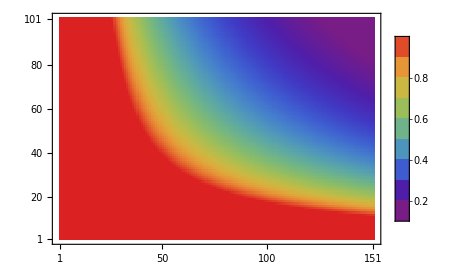

```mathematica
(*
NEW idea: mesh it myself (compute the function at set points) and plot the resultant (x, y, intensity data)
*)
mat2d=ConstantArray[0,{101,151}];
dyf[PeB_]:=(
For[j=1,j<102, ++j,
For[i=1,i<152,++i,
mat2d[[j,i]]=myiff[(i-1),PeB,(j-1)/100]
]
]
Return[mat2d]);
dyf[10];
MatrixPlot[mat2d,DataReversed->True,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0.2,1},{0,1}]]&),PlotRange->All,PlotLegends->
Range[0,1,0.1]]
(* A high value, 1, on the above plot indicates that nearly all particles are in the gaseous state *)
```

```mathematica
dyyf[PeB_]:=(
dyf[PeB];
MatrixPlot[mat2d,DataReversed->True,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0.2,1},{0,1}]]&),PlotRange->All,PlotLegends->
Range[0,1,0.1]]
)
```

```mathematica
man=Manipulate[dyyf[PeB],{PeB,0,150,10}]
```

```mathematica
(*ManToGif[man_,name_,step_]:=
Export[name<>".gif",Import[Export[name<>".mov",man],"ImageList"][[1;;-1;;step]]]
ManToGif[man, "/Users/kolbt/Desktop/PeB_plane_theory", 10]*)
```

```mathematica
(* Export["/Users/kolbt/Desktop/PeB_plane_theory.mov",man] *)
```

/Users/kolbt/Desktop/PeB_plane_theory.mov